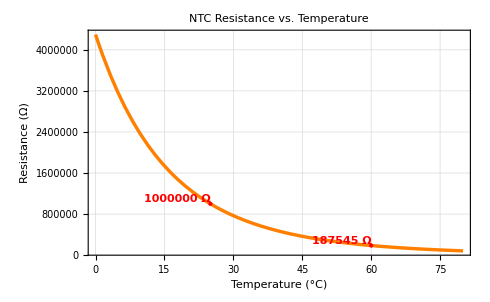

```mathematica
(*Parameters*)R25=1000000;(*Resistance at 25°C in ohms*)beta:=4750;(*Beta coefficient*)(*Function for the resistance at a temperature T in Kelvin*)R[T_]:=R25*Exp[beta*(1/T-1/298.15)]

(*Calculate resistances at 25°C and 60°C*)
resistanceAt25C=Round[R[25+273.15]];
resistanceAt60C=Round[R[60+273.15]];
(*Generate the plot in the range of 0°C to 80°C with markers at 25°C and 60°C*)
Plot[R[T+273.15],{T,0,80},PlotLabel->"NTC Resistance vs. Temperature",AxesLabel->{"Temperature (°C)","Resistance (Ω)"},PlotRange->All,GridLines->Automatic,Frame->True,PlotStyle->Directive[12,Thickness[0.005],Orange],LabelStyle->{12,Bold,Black},FrameLabel->{"Temperature (°C)","Resistance (Ω)"},Epilog->{Red,PointSize[Large],Point[{25,resistanceAt25C}],Point[{60,resistanceAt60C}],Text[Style[ToString[resistanceAt25C]<>" Ω",Red,Bold],{25,resistanceAt25C},{1,-1}],Text[Style[ToString[resistanceAt60C]<>" Ω",Red,Bold],{60,resistanceAt60C},{1,-1}]}]
```

```mathematica
VoltageTH:=0.45;
Current:=1 10^-6
(*Calculate R1*)
R1=VoltageTH/Current-Round[R[60+273.15]]
```

262455.

260000

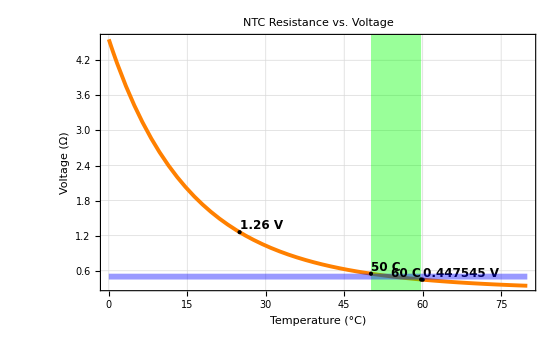

```mathematica
R1=260000
V[T_]:=Current*(R25*Exp[beta*(1/T-1/298.15)]+R1)
VThreshold=0.5;(*Voltage threshold*)
Hysteresis=0.1;(*Hysteresis value*)

(*Calculate resistances at 25°C and 60°C*)
voltageAt25C:=V[25+273.15];
voltageAt60C:=V[60+273.15];


(*Solve for T when V[T]=0.45 using Reduce*)tempAt0V45=T/.FindRoot[V[T]==VThreshold-Hysteresis/2,{T,300}];
tempAt0V55=T/.FindRoot[V[T]==VThreshold+Hysteresis/2,{T,300}];

(*Define the threshold voltages*)
VUpper=VThreshold+Hysteresis/2;
VLower=VThreshold-Hysteresis/2;

(*Generate the plot in the range of 0°C to 80°C with markers at 25°C and 60°C*)
Plot[V[T+273.15],{T,0,80},PlotLabel->"NTC Resistance vs. Voltage",PlotRange->All,GridLines->Automatic,Frame->True,PlotStyle->Directive[12,Thickness[0.005],Orange],LabelStyle->{12,Bold,Black},FrameLabel->{"Temperature (°C)","Voltage (Ω)"},Epilog->{
{Green,Opacity[0.4],Polygon[{{tempAt0V45-273.15,0},{tempAt0V55-273.15,0},{tempAt0V55-273.15,5},{tempAt0V45-273.15,5}}],Blue,Rectangle[{0,VThreshold-Hysteresis/2},{80,VThreshold+Hysteresis/2}]},
Black,PointSize[Large],Point[{25,voltageAt25C}],Point[{tempAt0V55-273.15,V[tempAt0V55]}],Point[{tempAt0V45-273.15,V[tempAt0V45]}],Point[{60,voltageAt60C}],Text[Style[ToString[voltageAt25C]<>" V",Black,12,Bold],{25,voltageAt25C},{-1,-1}],Text[Style[ToString[voltageAt60C]<>" V",Black,12,Bold],{60,voltageAt60C},{-1,-1}],Text[Style[ToString[Round[tempAt0V45-273.15]]<>" C",Black,12,Bold],{tempAt0V45-273.15,V[tempAt0V45]},{1,-5}],Text[Style[ToString[Round[tempAt0V55-273.15]]<>" C",Black,12,Bold],{tempAt0V55-273.15,V[tempAt0V55]},{-1,-5}]}]
```

```mathematica
(*Parameters*)R25=1000000;(*Resistance at 25°C in ohms*)VThreshold=0.5;(*Voltage threshold*)Hysteresis=0.1;(*Hysteresis value*)Current=1*10^-6;(*Current in Amperes*)VoltageTH=0.45;(*Voltage threshold for calculating R1*)(*Function to calculate R1*)calcR1[betaX_]:=Module[{R60,R1},R60=R25*Exp[betaX*(1/(60+273.15)-1/298.15)];
R1=VoltageTH/Current-Round[R60];
R1]

(*Voltage function*)
V[T_,betaX_]:=Current*(R25*Exp[betaX*(1/T-1/298.15)]+calcR1[betaX])

(*Solve for temperatures using FindRoot*)
tempAt0V45Beta[beta_]:=T/.Quiet[FindRoot[V[T,beta]==VThreshold-Hysteresis/2,{T,300}]]
tempAt0V55Beta[beta_]:=T/.Quiet[FindRoot[V[T,beta]==VThreshold+Hysteresis/2,{T,300}]]

(*Calculate voltages at specific temperatures*)
voltageAt25CBeta[beta_]:=V[25+273.15,beta]
voltageAt60CBeta[beta_]:=V[60+273.15,beta]

(*Generate the plot with a slider for beta*)
Manipulate[Module[{tAt0V45,tAt0V55,vAt25C,vAt60C},tAt0V45=tempAt0V45Beta[beta];
tAt0V55=tempAt0V55Beta[beta];
vAt25C=voltageAt25CBeta[beta];
vAt60C=voltageAt60CBeta[beta];
Plot[V[T+273.15,beta],{T,0,80},PlotLabel->"NTC Resistance vs. Voltage",PlotRange->All,GridLines->Automatic,Frame->True,PlotStyle->Directive[12,Thickness[0.005],Orange],LabelStyle->{12,Bold,Black},FrameLabel->{"Temperature (°C)","Voltage (V)"},Epilog->{{Green,Opacity[0.4],Polygon[{{tAt0V45-273.15,0},{tAt0V55-273.15,0},{tAt0V55-273.15,5},{tAt0V45-273.15,5}}],Blue,Rectangle[{0,VThreshold-Hysteresis/2},{80,VThreshold+Hysteresis/2}]},Black,PointSize[Large],Point[{25,vAt25C}],Point[{tAt0V55-273.15,V[tAt0V55,beta]}],Point[{tAt0V45-273.15,V[tAt0V45,beta]}],Point[{60,vAt60C}],Text[Style[ToString[vAt25C]<>" V",Black,12,Bold],{25,vAt25C},{-1,-1}],Text[Style[ToString[vAt60C]<>" V",Black,12,Bold],{60,vAt60C},{-1,-1}],Text[Style[ToString[Round[tAt0V45-273.15]]<>" C",Black,12,Bold],{tAt0V45-273.15,V[tAt0V45,beta]},{1,-5}],Text[Style[ToString[Round[tAt0V55-273.15]]<>" C",Black,12,Bold],{tAt0V55-273.15,V[tAt0V55,beta]},{-1,-5}]}]],{{beta,4350,"Beta"},1000,6000,250}]
```

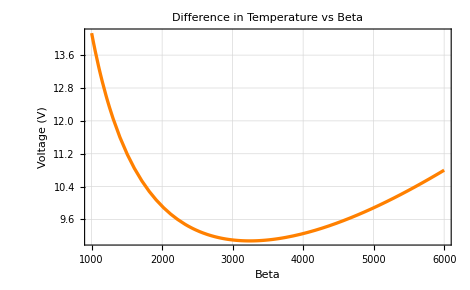

```mathematica
deltaTemp[beta_]:=tempAt0V45Beta[beta]-tempAt0V55Beta[beta];
Plot[deltaTemp[beta],{beta,1000,6000},AxesLabel->{"Beta","Difference in Temperature"},PlotLabel->"Difference in Temperature vs Beta",PlotRange->All,PlotRange->All,GridLines->Automatic,Frame->True,PlotStyle->Directive[12,Thickness[0.005],Orange],LabelStyle->{12,Bold,Black},FrameLabel->{"Beta","Voltage (V)"}]
```

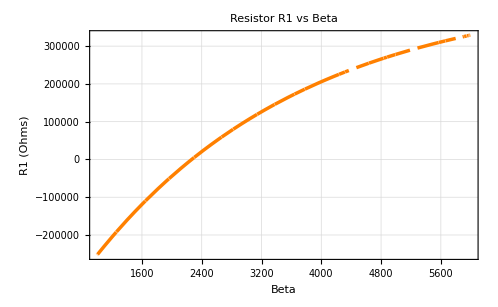

```mathematica
TemperatureBetaR1:=60;
R25Beta:=1000000;
RBeta[beta_]:=VoltageTH/Current-Round[R25Beta*Exp[beta*(1/(TemperatureBetaR1+273.15)-1/298.15)]];
Plot[RBeta[beta],{beta,1000,6000},PlotLabel->"Resistor R1 vs Beta",PlotRange->All,GridLines->Automatic,Frame->True,PlotStyle->Directive[12,Thickness[0.005],Orange],LabelStyle->{12,Bold,Black},FrameLabel->{"Beta","R1 (Ohms)"}]
```